# s-curve-beta: Efficient Python implementation of the smoothest S-curve robot motion planner ever

1. It’s 2022 and you’re still using a trapezoid motion profile?
2. Your robot is vibrating like a vacuum machine?
3. Tired of the mess in the code because of the multiple piecewise time regions?
4. Want a simple single-formula smooth motion profile?

If you answer “yes” to any of the above, read on.

Based on the answer of Cuye Waldman (https://math.stackexchange.com/a/2403818) I present this Python package to calculate the S-curve for the robot motion planning with a given maximum velocity and acceleration with a single formula.

Here is the complete motion formula:

```mathematica
f[x_,p_]:=1/2(1+RealSign[x]*Beta[x^2,1/2,p+1]/Beta[1/2,p+1])
motionTime[robotVmax_,robotAmax_,motionRange_]:=Max[(2*3^(3/4))/(√π)*√(motionRange/robotAmax),(32 motionRange)/(5 π robotVmax)]
position[t_,robotVmax_,robotAmax_,motionRange_]:=motionRange*f[(2t)/motionTime[robotVmax,robotAmax,motionRange]-1,2.5]
```

Let’s make some plots.

```mathematica
generatePlot[vmax_,amax_,range_,label_]:=Block[{tMax,text},
{
tMax=motionTime[vmax,amax,range];
text="(t, "~~ToString[vmax]~~", "~~ToString[amax]~~", "~~ToString[range]~~")";
Text[label],
Plot[position[x,vmax,amax,range],{x,0,tMax},ImageSize->400,AxesLabel->{"t",""},
Epilog->{ColorData[97,"ColorList"]⟦1⟧,PointSize[Large],Point[{tMax,range}],
Black,
Text["motionTime = "~~ToString[N[tMax]],{tMax,range-0.05},{1,1}]
}],
Plot[Evaluate@Table[D[position[x,vmax,amax,range],{x,i}],{i,1,3}],{x,0,tMax},ImageSize->400,PlotStyle->(ColorData[97,"ColorList"]⟦2;;⟧),AxesLabel->{"t",""},
Epilog->{Dashed,{
ColorData[97,"ColorList"]⟦3⟧,
InfiniteLine[{0,amax},{1,0}],Text["maximum acceleration ="~~ToString[amax],{0,amax},{-1,-1}],
ColorData[97,"ColorList"]⟦2⟧,
InfiniteLine[{0,vmax},{1,0}],Text["maximum velocity ="~~ToString[vmax],{tMax,vmax},{1,-1}]
}}
],
LineLegend[ColorData[97,"ColorList"]⟦;;4⟧,#~~text&/@{"position pos","velocity pos'","acceleration pos''","jerk pos'''"}]
}
]
```

Here are 2 examples of motion planning with motionRange=2:

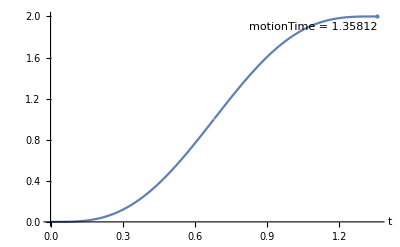
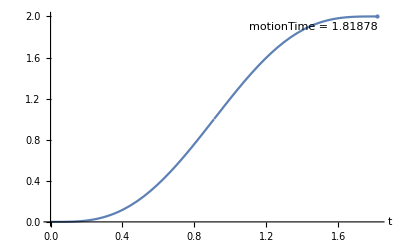
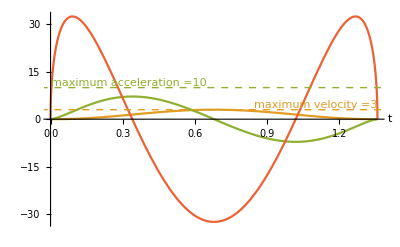
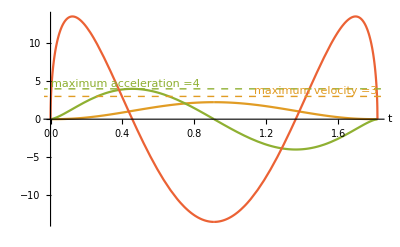
Example of motion where motionTime
is limited by max velocity | Example of motion where motionTime
is limited by max acceleration
-Graphics- | -Graphics-
-Graphics- | -Graphics-
 |

```mathematica
Grid[Transpose[{
generatePlot[3,10,2,"Example of motion where motionTime\nis limited by max velocity"],
generatePlot[3,4,2,"Example of motion where motionTime\nis limited by max acceleration"]
}]
]
```

The motion curve always has the same shape, while horizontal and vertical scales change. This property has the following benefits:
1. The maximum jerk is smaller compared to the case where you accelerate to the maximum velocity, stay there for a while and then decelerate.
2. The curve (function f(t,2.5) for -1<=t<=1)can be precomputed, so instead of calculating Beta functions each time it’s possible to do the linear interpolation of the precomputed points.

# Multiple axes synchronization

To synchronize multiple axes simply calculate the maximum motion time of all axes and use it for every axis. This will minimize maximum jerk and acceleration of the initially faster axes, decreasing the vibrations of the robot.

# Derivations

The original f function comes from the integration of the superparabola, done by Cuye Waldman. We can prove that his integration is correct:

```mathematica
FullSimplify[Integrate[((1-x^2)^p)/Beta[1/2,1+p],{x,-1,t}]-f[t,p],Element[p,Reals]&&Element[t,Reals]&&0<=t<1&&p>-1]
```

0

f gives 0 and 1 at the beginning and end (here time goes from -1 to 1):

```mathematica
{f[x,0],f[x,1],f[x,2.5],f[x,5],f[x,100]}/.x->{-1,1}
```

{{0,1},{0,1},{0.,1.},{0,1},{0,1}}

Example plot of f:

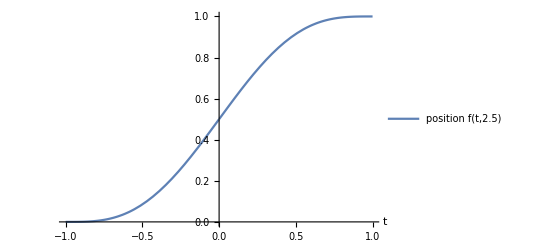
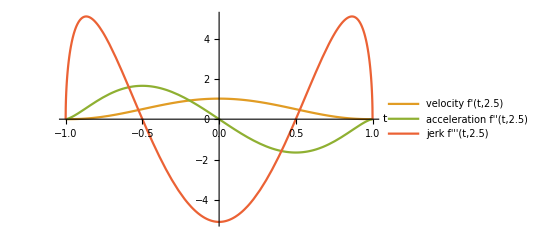

```mathematica
Column[{
Plot[f[x,2.5],{x,-1,1},ImageSize->400,PlotLegends->{"position f(t,2.5)"},AxesLabel->{"t",""}],
Plot[Evaluate@Table[D[f[x,2.5],{x,i}],{i,1,3}],{x,-1,1},PlotLegends->{"velocity f'(t,2.5)","acceleration f''(t,2.5)","jerk f'''(t,2.5)"},ImageSize->400,PlotStyle->(ColorData[97,"ColorList"]⟦2;;⟧),AxesLabel->{"t",""}]
}]
```

### Proof that the most optimal p is 2.5

My suggested value of p is 2.5 which gives the lowest possible absolute jerk, let’s see why.

Visualizing derivatives with different values of p:

```mathematica
Animate[
Show[
Plot[Evaluate@Table[D[f[x,2.5],{x,i}],{i,0,3}],{x,-1,1},PlotLegends->{"position f(t,2.5)","velocity f'(t,2.5)","acceleration f''(t,2.5)","jerk f'''(t,2.5)"},PlotRange->{-11,8},PlotLabel->"p = "~~ToString[param]],
Plot[Evaluate@Table[D[f[x,param],{x,i}],{i,0,3}],{x,-1,1},PlotLegends->(StringJoin[#,"(t,"~~ToString[param]~~")"]&/@{"position f","velocity f'","acceleration f''","jerk f'''"}),PlotRange->All,PlotStyle->Dashed]
],
{param,2.00001,5,0.15}]
```

Calculating largest jerks for different values of the parameter p:

```mathematica
jerkValues[param_]:={Limit[D[f[x,param],{x,3}],x->0],
Maximize[{D[f[x,param],{x,3}],-1<=x<=1},x]⟦1⟧}
```

```mathematica
Manipulate[Plot[Evaluate@Table[D[f[x,param],{x,i}],{i,0,3}],{x,-1,1},PlotLegends->{"f","f'","f''","f'''"},PlotRange->All,
Epilog->{Dashed,InfiniteLine[{-1,#},{1,0}]&/@jerkValues[param]}],
{{param,3.1},2.001,5}]
```

```mathematica
paramData=Table[{p,jerkValues[p]},{p,2.001,3,0.01}];
```

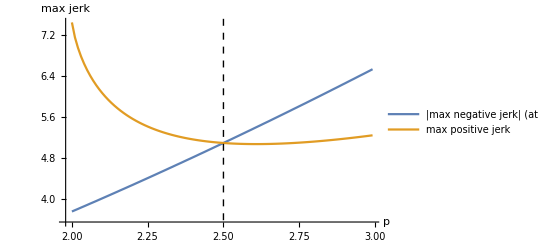

```mathematica
ListLinePlot[Abs[Transpose[(Outer[List,{#1},#2]⟦1⟧&@@@paramData)]],PlotLegends->{"|max negative jerk| (at x=0)","max positive jerk"},Epilog->{Dashed,InfiniteLine[{2.5,0},{0,1}]},AxesLabel->{"p","max jerk"}]
```

The best value of the parameter p happens to be 2.5, where the max absolute jerk is the smallest.

#### Discussion on 2<=p<=2.5

It’s possible to achieve slightly lower maximum robot accelerations at 2<=p<=2.5:

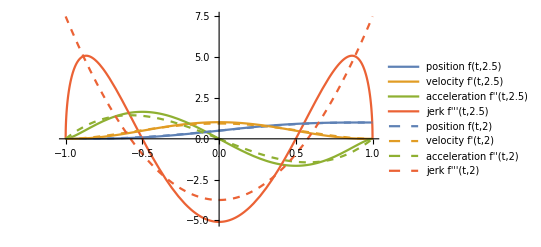

```mathematica
param=2;
Show[
Plot[Evaluate@Table[D[f[x,2.5],{x,i}],{i,0,3}],{x,-1,1},PlotLegends->{"position f(t,2.5)","velocity f'(t,2.5)","acceleration f''(t,2.5)","jerk f'''(t,2.5)"},PlotRange->All],
Plot[Evaluate@Table[D[f[x,param],{x,i}],{i,0,3}],{x,-1,1},PlotLegends->(StringJoin[#,"(t,"~~ToString[param]~~")"]&/@{"position f","velocity f'","acceleration f''","jerk f'''"}),PlotRange->All,PlotStyle->Dashed]
]
```

Using 2<=p<=2.5 can shorten the robot motion time a little bit at the cost of increased maximum jerk hence increased robot vibrations at the beginning and at the end of the motion. I have decided not to implement this at the moment.

### Rescaling function f for the particular motion parameters

#### 1. Motion time from the maximum velocity constraint

Max velocity at t=0:

```mathematica
maxVelocity=Limit[D[f[x,5/2],x],x->0]
```

16/(5 π)

With the given maximum robot velocity robotVmax the shortest motion time can be derived from the equation:

```mathematica
Solve[robotVmax==(2*16/(5Pi)*motionRange)/time,time]
```

{{time→(32 motionRange)/(5 π robotVmax)}}

#### 2. Motion time from the maximum acceleration constraint

Calculate max acceleration at p=2.5:

```mathematica
FindMaximum[{D[f[x,5/2],{x,2}],-1<x<0},x]
```

{1.65399,{x→-0.5}}

Maximum acceleration happens to be at t=-1/2

```mathematica
maxAcceleration=D[f[x,5/2],{x,2}]/.x->-1/2
```

(3 √3)/π

With the given maximum robot acceleration robotAmax the shortest motion time can be derived from the equation:

robotAmax=(4(3 √3)/π motionRange)/time^2,

where time is the total duration of robot motion.

Let’s solve the equation and pick the solution where time>0:

```mathematica
Solve[robotAmax==(4*(3 √3)/π motionRange)/time^2,time]
```

{{time→-(2 3^(3/4) √motionRange)/(√π √robotAmax)},{time→(2 3^(3/4) √motionRange)/(√π √robotAmax)}}

#### 3. Motion time with both constraints

To consider both maximum velocity and maximum acceleration constraints we have to take the maximum of the above motion times:

```mathematica
motionTime[robotVmax_,robotAmax_,motionRange_]:=Max[(2*3^(3/4))/(√π)*√(motionRange/robotAmax),(32 motionRange)/(5 π robotVmax)]
```

In the future I may add a maximum jerk constraint.

#### 4. Final motion position formula

We have to rescale t in f(t,2.5) in such a way that the motion would start at t=0  and end at t=motionTime. Additionally we have to rescale the value of f to go from 0 to motionRange. After rescaling we get:

```mathematica
position[t_,robotVmax_,robotAmax_,motionRange_]:=motionRange*f[(2t)/motionTime[robotVmax,robotAmax,motionRange]-1,2.5]
```

### Example robot motions limited by acceleration

Almost unlimited maximum velocity (robotVmax=100):

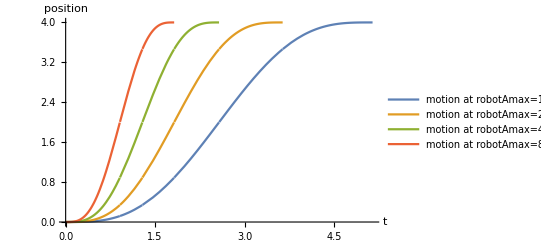
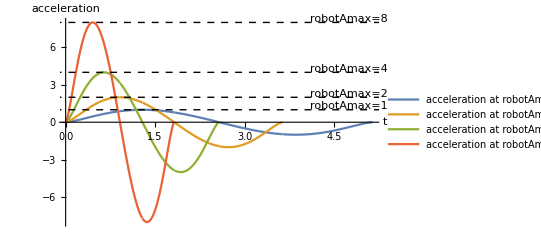

```mathematica
robotAmaxArray={1,2,4,8};
Vmax=100;
desiredMotionRange=4;
tMax=motionTime[Vmax,Min[robotAmaxArray],desiredMotionRange];
Column[{
Plot[Evaluate[position[t,Vmax,#,desiredMotionRange]&/@robotAmaxArray],{t,0,tMax},ImageSize->400,
PlotLegends->{"motion at robotAmax="~~ToString[#]&/@robotAmaxArray},
AxesLabel->{"t","position"}],
Plot[Evaluate[D[position[t,Vmax,#,desiredMotionRange],{t,2}]&/@robotAmaxArray],{t,0,tMax},ImageSize->400,
Epilog->{Dashed,{InfiniteLine[{0,#},{1,0}],Text["robotAmax="~~ToString[#],{tMax-0.4,#+0.3}]}&/@robotAmaxArray},
PlotLegends->{"acceleration at robotAmax="~~ToString[#]&/@robotAmaxArray},
AxesLabel->{"t","acceleration"}
]
}]
```